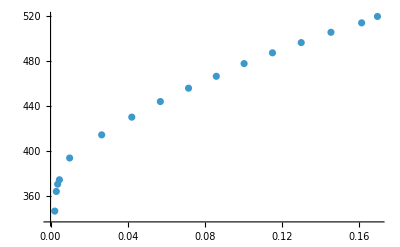

{a→107.031,b→450.339,c→-1996.24,d→1122.7,e→278.518}

278.518+107.031 (1-ⅇ^(-450.339 t))+1122.7 t-1996.24 t^2

385.549-107.031 ⅇ^(-450.339 t)+1122.7 t-1996.24 t^2

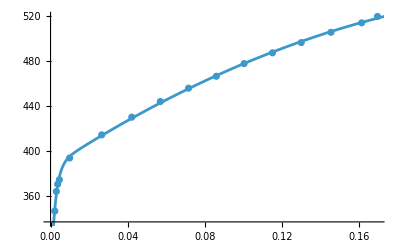

```mathematica
(*1) Importa e higieniza*)
data=Import["/home/diogo/Dropbox/mathematica/modifications-bc/A500_t16_tensile.csv"];
data=Delete[data,1];
data2=Table[{data[[i]][[2]],data[[i]][[1]]},{i,20,Length[data]}];
data2=DeleteDuplicates[data2];
For[k=1,k<=4,k++,
For[j=1,j<Length[data2],j++,
For[i=1,i<Length[data2],i++,
If[data2[[i]][[1]]==data2[[j]][[1]],
data2=Delete[data2,i];
];
If[data2[[i]][[2]]<330,
data2=Delete[data2,i];
];
];
];
];
ListPlot[data2]
f[t_]:=(a(1-Exp[-b t ])+c t^2+d t+e)
fit=FindFit[data2,f[t],{a,b,c,d,e},t]
ff=f[t]/.fit
(278.51775588600316+107.03078301291825 (1-ⅇ^(-450.3386387920765 t))+1122.6997583510627 t-1996.235137824671 t^2)//Simplify
Show[ListPlot[data2],Plot[ff,{t,0,0.25},PlotRange->All]]
```